```mathematica
NotebookDirectory[]
```

/home/carlos/Documentos/Programacion/Fisica-Mathematica/Computer_Science/

```mathematica
Token[symbol_String,name_String]:=<|"Class"->"Token","Symbol"->symbol,"Name"->name|>;
```

```mathematica
TokenKeyword[symbol_String,name_String]:=<|"Class"->"TokenKeyword","Symbol"->symbol,"Name"->name|>;
```

```mathematica
tokenSymbols = Map[
Token[#[[1]],#[[2]]]&,
{
{"end of file","EndOfFile"},
{":=", "Assign"},
{"*", "Asterisk"},
{":", "Colon"},
{"!=", "Different"},
{"=", "Equal"},
{"(", "LeftParenthesis"},
{"-", "Minus"},
{"+", "Plus"},
{")", "RightParenthesis"},
{";", "Semicolon"},
{"/", "Slash"},
{"%", "Percent"},
{">", "Greater"},
{">=", "GreaterOrEqual"},
{"<", "Lower"},
{"<=", "LowerOrEqual"}
}
];
tokenIdentifiersAndLiterals = Map[
Token[#[[1]],#[[2]]]&,
{
{"identifier", "Identifier"},
{"integer literal", "IntegerLiteral"},
{"real literal", "RealLiteral"},
{"string literal", "StringLiteral"}
}
];

tokenKeywords = Map[
TokenKeyword[#[[1]],#[[2]]]&,
{
{"and","And"},
{"do", "Do"},
{"else", "Else"},
{"end", "End"},
{"float", "Float"},
{"for", "For"},
{"if", "If"},
{"int", "Int"},
{"not", "Not"},
{"or", "Or"},
{"read", "Read"},
{"then", "Then"},
{"to", "To"},
{"var", "Var"},
{"while", "While"},
{"write", "Write"}
}
];
```

```mathematica
tinyProgram ="var i : int;
for i := 0 to 10 do     # this is a comment
   write i;
end";
```

```mathematica
tokenSymbolsNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenSymbols]]];
tokenSymbolsDFA = NFAToDFA[tokenSymbolsNFA];
```

```mathematica
keywordNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenKeywords]]];
keywordDFA = NFAToDFA[keywordNFA];
```

```mathematica
RegexCompute[keywordDFA,"if"]
```

{{{<|Node→1|>},{<|Parent→1,Node→11,InputSymbol→{i}|>},{<|Parent→11,Node→26,InputSymbol→{f}|>}},True,{If}}

## Basura

```mathematica
tokenIdentifiersAndLiterals = Map[
Token[#[[1]],#[[2]]]&,
{
{"identifier", "Identifier"},
{"integer literal", "IntegerLiteral"},
{"real literal", "RealLiteral"},
{"string literal", "StringLiteral"}
}
];
```

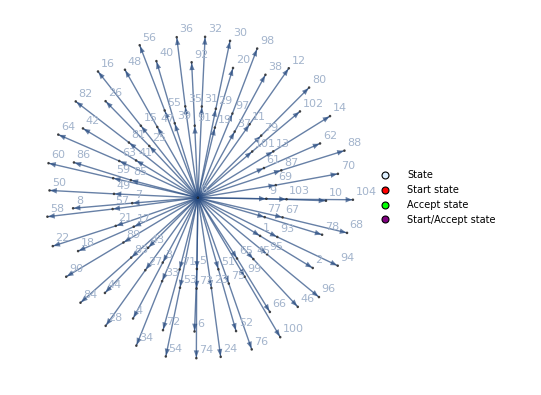

```mathematica
FAPlot[RegexAlphabet[],"Labeled"->False]
```

```mathematica
dfaAlphabet = NFAToDFA[RegexAlphabet[]];
```

```mathematica
dfaDigits = NFAToDFA[RegexDigits[]];
```

```mathematica
identifierRegex =NFAToDFA[RegexUnion[RegexAlphabet[],RegexStar[RegexUnion[RegexAlphabet[],RegexDigits[]]]]];
```

```mathematica
machine = RegexUnion[RegexAlphabet[],RegexStar[RegexUnion[RegexAlphabet[],RegexDigits[]]]];
```

```mathematica
RegexCompute[identifierRegex,"hola"][[2]]
```

True

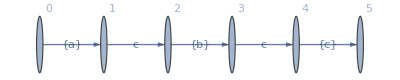

```mathematica
FAPlot[Regex["abc"],"Labeled"->False]
```

```mathematica
FAPlot@RegexUnion[Regex["a"],Regex["b"],Regex["c"]]
```

```mathematica
Manipulate[FAPlot[Apply[RegexUnion,Map[Regex,Take[Alphabet[],i]]],"Labeled"->False],{{i,3},2,Length[Alphabet[]],1}]
```

```mathematica
nfa = Apply[RegexUnion,Map[Regex,Alphabet[]]];
```

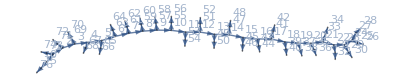

```mathematica
FAPlot[nfa,"Labeled"->False]
```

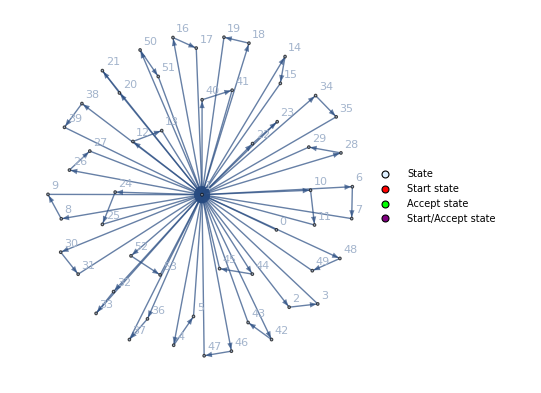

```mathematica
FAPlot[RegexStar[SimplifyMachine[nfa]],"Labeled"->False]
```

```mathematica
RegexCompute[SimplifyMachine[RegexStar[RegexAlphabet[]]],"Hola"]
```

{{{<|Node→0|>,<|Parent→0,Node→51,InputSymbol→ϵ|>,<|Parent→0,Node→103,InputSymbol→ϵ|>,<|Parent→0,Node→49,InputSymbol→ϵ|>,<|Parent→0,Node→101,InputSymbol→ϵ|>,<|Parent→0,Node→47,InputSymbol→ϵ|>,<|Parent→0,Node→99,InputSymbol→ϵ|>,<|Parent→0,Node→45,InputSymbol→ϵ|>,<|Parent→0,Node→97,InputSymbol→ϵ|>,<|Parent→0,Node→43,InputSymbol→ϵ|>,<|Parent→0,Node→95,InputSymbol→ϵ|>,<|Parent→0,Node→41,InputSymbol→ϵ|>,<|Parent→0,Node→93,InputSymbol→ϵ|>,<|Parent→0,Node→39,InputSymbol→ϵ|>,<|Parent→0,Node→91,InputSymbol→ϵ|>,<|Parent→0,Node→37,InputSymbol→ϵ|>,<|Parent→0,Node→89,InputSymbol→ϵ|>,<|Parent→0,Node→35,InputSymbol→ϵ|>,<|Parent→0,Node→87,InputSymbol→ϵ|>,<|Parent→0,Node→33,InputSymbol→ϵ|>,<|Parent→0,Node→85,InputSymbol→ϵ|>,<|Parent→0,Node→31,InputSymbol→ϵ|>,<|Parent→0,Node→83,InputSymbol→ϵ|>,<|Parent→0,Node→29,InputSymbol→ϵ|>,<|Parent→0,Node→81,InputSymbol→ϵ|>,<|Parent→0,Node→27,InputSymbol→ϵ|>,<|Parent→0,Node→79,InputSymbol→ϵ|>,<|Parent→0,Node→25,InputSymbol→ϵ|>,<|Parent→0,Node→77,InputSymbol→ϵ|>,<|Parent→0,Node→23,InputSymbol→ϵ|>,<|Parent→0,Node→75,InputSymbol→ϵ|>,<|Parent→0,Node→21,InputSymbol→ϵ|>,<|Parent→0,Node→73,InputSymbol→ϵ|>,<|Parent→0,Node→19,InputSymbol→ϵ|>,<|Parent→0,Node→71,InputSymbol→ϵ|>,<|Parent→0,Node→17,InputSymbol→ϵ|>,<|Parent→0,Node→69,InputSymbol→ϵ|>,<|Parent→0,Node→15,InputSymbol→ϵ|>,<|Parent→0,Node→67,InputSymbol→ϵ|>,<|Parent→0,Node→13,InputSymbol→ϵ|>,<|Parent→0,Node→65,InputSymbol→ϵ|>,<|Parent→0,Node→11,InputSymbol→ϵ|>,<|Parent→0,Node→63,InputSymbol→ϵ|>,<|Parent→0,Node→9,InputSymbol→ϵ|>,<|Parent→0,Node→61,InputSymbol→ϵ|>,<|Parent→0,Node→7,InputSymbol→ϵ|>,<|Parent→0,Node→59,InputSymbol→ϵ|>,<|Parent→0,Node→5,InputSymbol→ϵ|>,<|Parent→0,Node→57,InputSymbol→ϵ|>,<|Parent→0,Node→1,InputSymbol→ϵ|>,<|Parent→0,Node→3,InputSymbol→ϵ|>,<|Parent→0,Node→53,InputSymbol→ϵ|>,<|Parent→0,Node→55,InputSymbol→ϵ|>},{<|Parent→67,Node→68,InputSymbol→{H}|>,<|Parent→68,Node→51,InputSymbol→ϵ|>},{},{},{}},False,{}}